```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(*max = 6.0001;*)
max=1.0;

(*s1=1+241*120;
s2=241*121;*)

s1=1+481*240;
s2=481*241;
```

```mathematica
dx= 0.01;
pts=1/dx;

DarkBlueBlueBlend=Table[Blend[{Darker[Blue],Blue},dx*i],{i,0,pts-1}];
BlueCyanBlend=Table[Blend[{Blue,Cyan},dx*i],{i,0,pts-1}];
CyanGreenBlend=Table[Blend[{Cyan,Green},dx*i],{i,0,pts-1}];
GreenYellowBlend=Table[Blend[{Green,Yellow},dx*i],{i,0,pts-1}];
YellowOrangeBlend=Table[Blend[{Yellow,Orange},dx*i],{i,0,pts-1}];
OrangeRedBlend=Table[Blend[{Orange,Red},dx*i],{i,0,pts-1}];
RedDarkRedBlend=Table[Blend[{Red,Darker[Red]},dx*i],{i,0,pts}];

colors=Flatten[{DarkBlueBlueBlend, BlueCyanBlend, CyanGreenBlend, GreenYellowBlend, YellowOrangeBlend, OrangeRedBlend,RedDarkRedBlend}];

colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Jet"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

BarLegend[{ColorData["Jet"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
```

```mathematica
e1=Take[Import[wd<>"/../../output/e_0.250.dat"]][[All,{1,2,4}]];
e2=Take[Import[wd<>"/../../output/e_1.250.dat"]][[All,{1,2,4}]];
e3=Take[Import[wd<>"/../../output/e_2.250.dat"]][[All,{1,2,4}]];
(*e4=Take[Import[wd<>"/../../output/e_3.250.dat"]][[All,{1,2,4}]];
e5=Take[Import[wd<>"/../../output/e_4.250.dat"]][[All,{1,2,4}]];
e6=Take[Import[wd<>"/../../output/e_5.250.dat"]][[All,{1,2,4}]];
e7=Take[Import[wd<>"/../../output/e_6.250.dat"]][[All,{1,2,4}]];*)

ux1=Take[Import[wd<>"/../../output/ux_0.250.dat"]][[All,{1,2,4}]];
ux2=Take[Import[wd<>"/../../output/ux_1.250.dat"]][[All,{1,2,4}]];
ux3=Take[Import[wd<>"/../../output/ux_2.250.dat"]][[All,{1,2,4}]];
(*ux4=Take[Import[wd<>"/../../output/ux_3.250.dat"]][[All,{1,2,4}]];
ux5=Take[Import[wd<>"/../../output/ux_4.250.dat"]][[All,{1,2,4}]];
ux6=Take[Import[wd<>"/../../output/ux_5.250.dat"]][[All,{1,2,4}]];
ux7=Take[Import[wd<>"/../../output/ux_6.250.dat"]][[All,{1,2,4}]];*)
```

9167.69

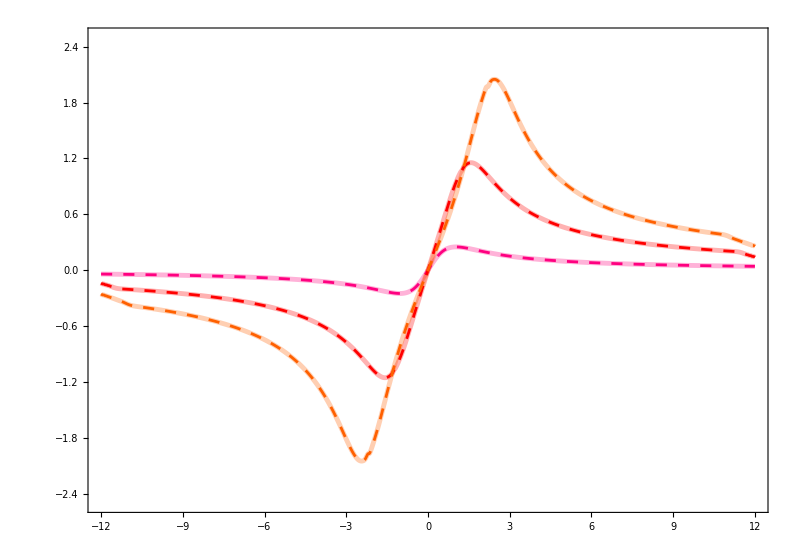

```mathematica
emax=Max[e1[[1;;All,3]]]
(*emin=Min[e7[[1;;All,3]]];*)
(*uxmax=Max[ux7[[1;;All,3]]]*)

(* Replace with exact solution *)
e1test=e1[[s1;;s2,{1,3}]];
e2test=e2[[s1;;s2,{1,3}]];
e3test=e3[[s1;;s2,{1,3}]];
(*e4test=e4[[s1;;s2,{1,3}]];
e5test=e5[[s1;;s2,{1,3}]];
e6test=e6[[s1;;s2,{1,3}]];
e7test=e7[[s1;;s2,{1,3}]];*)

ux1test=ux1[[s1;;s2,{1,3}]];
ux2test=ux2[[s1;;s2,{1,3}]];
ux3test=ux3[[s1;;s2,{1,3}]];
(*ux4test=ux4[[s1;;s2,{1,3}]];
ux5test=ux5[[s1;;s2,{1,3}]];
ux6test=ux6[[s1;;s2,{1,3}]];
ux7test=ux7[[s1;;s2,{1,3}]];*)


e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
(*e4slice=e4[[s1;;s2,{1,3}]];
e5slice=e5[[s1;;s2,{1,3}]];
e6slice=e6[[s1;;s2,{1,3}]];
e7slice=e7[[s1;;s2,{1,3}]];*)

ux1slice=ux1[[s1;;s2,{1,3}]];
ux2slice=ux2[[s1;;s2,{1,3}]];
ux3slice=ux3[[s1;;s2,{1,3}]];
(*ux4slice=ux4[[s1;;s2,{1,3}]];
ux5slice=ux5[[s1;;s2,{1,3}]];
ux6slice=ux6[[s1;;s2,{1,3}]];
ux7slice=ux7[[s1;;s2,{1,3}]];*)

(*blue=RGBColor[0,0.3,1]*)
(*purple=RGBColor[0.7,0,0.6]*)
(*RGBColor[0,0.8,0.4]*)

magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[3.5],Opacity[0.3]};
redTran={Red,AbsoluteThickness[3.5],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[3.5],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[3.5],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[3.5],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[3.5],Opacity[0.3]};
purpleTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[3.5],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};


style={magentaTran,redTran,orangeTran,(*greenTran,cyanTran,blueTran,purpleTran,*)magenta,red,orange(*,green,cyan,blue,purple*)};


ListPlot[{e1test},Joined->True,InterpolationOrder->2,PlotRange->All];
Export[wd<>"/e1_slice.png",%];

ListLogPlot[{e1test,e2test,e3test,(*e4test,e5test,e6test,e7test,*)e1slice,e2slice,e3slice(*,e4slice,e5slice,e6slice,e7slice*)},Joined->True,InterpolationOrder->2,PlotRange->{{-12,12},{0.001,1.1*emax}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->800];
Export[wd<>"/energy_slice.png",%];


ListPlot[{ux1test,ux2test,ux3test,(*ux4test,ux5test,ux6test,ux7test,*)ux1slice,ux2slice,ux3slice(*,ux4slice,ux5slice,ux6slice,ux7slice*)},Joined->True,InterpolationOrder->2,PlotRange->{{-12,12},{-2.5,2.5}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->800]
Export[wd<>"/ux_slice.eps",%];
```

```mathematica
(*

Grid[{{ListDensityPlot[e1,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Jet"],{0,1200}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Left],ColorFunction->ColorData["Jet"],ColorFunctionScaling->True,FrameStyle->Black,BaseStyle->14,ImageSize->400]}}];

Export[wd<>"/energy.png",%];*)
```

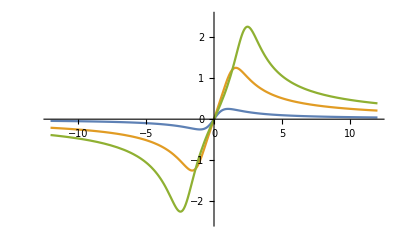

```mathematica
(* Analytic Solution for Flow Velocity *)



q=1.0;

κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*Abs[r])/(1.0+q^2*(τ^2+r^2))];

ux[τ_,r_]:=Sinh[κ[τ,r]]*Sign[r];

Plot[{ux[0.25,x],ux[1.25,x],ux[2.25,x]},{x,-12,12},PlotRange->{-2.5,2.5}]
```